```mathematica
(ag = {{0,0,0,0,2},{0,0,0,1,0},{2,0,0,2,0},{0,1,0,0,0},{2,0,0,0,0}}) // MatrixForm
```

(0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 1 | 0
2 | 0 | 0 | 2 | 0
0 | 1 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0)

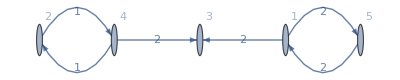

```mathematica
g = WeightedAdjacencyGraph[agᵀ /. {0 -> ∞}, VertexLabels->Automatic, EdgeLabels->"EdgeWeight"]
```

Inzidenzmatrix:

```mathematica
(n=IncidenceMatrix[g])//MatrixForm
```

(-1 | -1 | 0 | 0 | 0 | 1
0 | 0 | -1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | -1 | -1 | 0
0 | 1 | 0 | 0 | 0 | -1)

Stark zusammenhängende Teilgraphen:

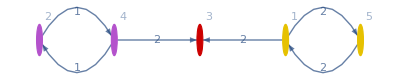

```mathematica
HighlightGraph[g, ConnectedComponents[g]]
```

Gradmatrix:

```mathematica
(dg = DiagonalMatrix[Total[ag, {2}]])//MatrixForm
```

(2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 2)

Laplace Matrix:

```mathematica
(lg=dg-ag)//MatrixForm
```

(2 | 0 | 0 | 0 | -2
0 | 1 | 0 | -1 | 0
-2 | 0 | 4 | -2 | 0
0 | -1 | 0 | 1 | 0
-2 | 0 | 0 | 0 | 2)

Laplace Spektrum:

```mathematica
σg=Eigenvalues[lg]
```

{4,4,2,0,0}